```mathematica
SetDirectory@NotebookDirectory[]
```

/home/nina/potts

```mathematica
data=Import["./output/ctags"<>ToString[100(#-1)]<>".out","Table"]&/@Range[30];
```

```mathematica
Length[DeleteDuplicates[Flatten@data[[30]]]]
```

1157

```mathematica
Export["gif.gif",Map[Colorize,data]]
```

gif.gif

```mathematica
data=Import["./axon/ctags1.out","Table"];
types=First@Import["./axon/types.out","Table"];
conts=Import["./axon/contactM0.out","Table"];
```

```mathematica
data=Import["./output/ctags1.out","Table"];
types=First@Import["./output/types.out","Table"];
conts=Import["./output/contactM0.out","Table"];
```

```mathematica
name="CH";
```

```mathematica
(*Import["./output/ctags"<>name<>".out","Table"]//Colorize*)
```

```mathematica
hor=Map[If[#==0,0,1]&,data[[2;;]]-data[[;;-2]],{2}];
vert=Map[If[#==0,0,1]&,data[[;;,2;;]]-data[[;;,;;-2]],{2}];
```

```mathematica
bord=Map[If[#==0,0,1]&,ArrayPad[hor,{{1,0},{0,0}}]+ArrayPad[hor,{{0,1},{0,0}}]+ArrayPad[vert,{{0,0},{1,0}}]+ArrayPad[vert,{{0,0},{0,1}}],{2}];
```

```mathematica
contsCM=Map[If[#>0&&types[[#]]==1,1,0]&,data,{2}]conts bord;
contsFB=Map[If[#>0&&types[[#]]==2,1,0]&,data,{2}]conts bord;
```

```mathematica
Ncm=Length@Position[types,1];
Nfb=Length@Position[types,2];
```

```mathematica
{Total[Flatten@contsCM]/Ncm,Total[Flatten@contsFB]/Nfb}//N
```

{0.,0.}

```mathematica
indexesCM=Map[If[#>0&&types[[#]]==1,#,0]&,data,{2}];
indexesFB=Map[If[#>0&&types[[#]]==2,#,0]&,data,{2}];
```

```mathematica
colorsCM=ColorSeparate[Colorize@indexesCM];
colorsFB=ColorSeparate[Colorize@indexesFB];
```

```mathematica
cell=Map[If[#==1,1,0]&,data,{2}];
```

```mathematica
core=Position[Map[If[#==0,0,1]&,Total[cellᵀ]],1][[3;;-3,1]];
```

```mathematica
{w,h}=Dimensions[cell];
```

```mathematica
maxC=Max[data];
```

```mathematica
min=SparseArray[Table[i->w,{i,1,maxC}]];
max=SparseArray[Table[i->0,{i,1,maxC}]];
```

```mathematica
Table[Module[{c=indexes[[i,j]]},
If[c≠0,
If[i<min[[c]],min[[c]]=i];
If[i>max[[c]],max[[c]]=i];
]],{i,1,w},{j,1,h}];
```

```mathematica
conts=indexes;
```

```mathematica
Table[Module[{c=indexes[[i,j]]},
If[c≠0,
If[0≤i-min[[c]]≤3,conts[[i,j]]=1,If[0≤max[[c]]-i≤3,conts[[i,j]]=1,conts[[i,j]]=0]];
]],{i,1,w},{j,1,h}];
```

```mathematica
Length[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]
```

39

```mathematica
ColorCombine[{colorsCM[[1]],Image@(contsCM bord+0.1ImageData[colorsCM[[2]]]+0.1ImageData[colorsFB[[2]]]),colorsFB[[3]]}]
```

-Graphics-

-Graphics-

```mathematica
indexes=data
```

```mathematica
mCM=Map[If[#>0&&types[[#]]==1,#,0]&,indexes,{2}];
mFB=Map[If[#>0&&types[[#]]==2,#,0]&,indexes,{2}];
(*F[x_]:={Mean[x],StandardDeviation[x]};*)
F[x_]:=Mean[x];
legsC=Table[Module[{mCell=Map[If[#==n,0,1]&,indexes,{2}]},{n,CountLegs[ImageCrop@Image[mCellᵀ]],types[[n]]}],{n,1,Length@types-1}];
legsCM=Select[legsC,#[[3]]==1&][[;;,2]];
legsFB=Select[legsC,#[[3]]==2&][[;;,2]];
```

```mathematica
hor=Map[If[#==0,0,1]&,indexes[[2;;]]-indexes[[;;-2]],{2}];
vert=Map[If[#==0,0,1]&,indexes[[;;,2;;]]-indexes[[;;,;;-2]],{2}];
bord=Map[If[#==0,0,1]&,ArrayPad[hor,{{1,0},{0,0}}]+ArrayPad[hor,{{0,1},{0,0}}]+ArrayPad[vert,{{0,0},{1,0}}]+ArrayPad[vert,{{0,0},{0,1}}],{2}];
contsCM=Map[If[#>0&&types[[#]]==1,1,0]&,indexes,{2}]conts bord;
contsFB=Map[If[#>0&&types[[#]]==2,1,0]&,indexes,{2}]conts bord;
Ncm=Length@Position[types,1];
Nfb=Length@Position[types,2];
zeros=Total[Flatten@Map[If[#==0,1,0]&,indexes[[50;;-50,50;;-50]],{2}]];
```

```mathematica
params=<<"params.txt";
```

```mathematica
Colorize@mFB
```

-Graphics-

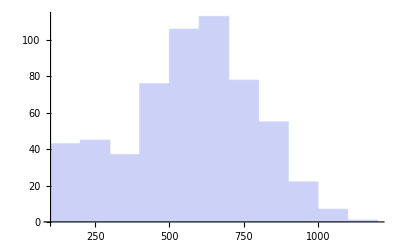

```mathematica
Histogram@(ComponentMeasurements[mCM,"Area"][[;;,2]]2.5^2)
```

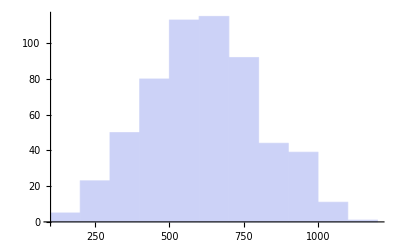

```mathematica
Histogram@(ComponentMeasurements[mFB,"Area"][[;;,2]]2.5^2)
```

```mathematica
800 800
```

640000

```mathematica
800 800/0.
```

```mathematica
Total@(ComponentMeasurements[mCM,"Area"][[;;,2]]2.5^2)+Total@(ComponentMeasurements[mFB,"Area"][[;;,2]]2.5^2)
```

1.03121×10^6

```mathematica
newline={params[[3;;]],{F@(ComponentMeasurements[mCM,"Area"][[;;,2]]2.5^2),
F[ComponentMeasurements[mCM,"ConvexCoverage"][[;;,2]]],
F[(1-ComponentMeasurements[mCM,"CaliperElongation"][[;;,2]])^-1],N@F[legsCM],Total[Flatten@contsCM]/Ncm}, 
{F@(ComponentMeasurements[mFB,"Area"][[;;,2]]2.5^2),
F[ComponentMeasurements[mFB,"ConvexCoverage"][[;;,2]]],
F[(1-ComponentMeasurements[mFB,"CaliperElongation"][[;;,2]])^-1],N@F[legsFB],Total[Flatten@contsFB]/Nfb},{zeros}};
```

```mathematica
17 68
```

1156

```mathematica
Length@DeleteDuplicates[Flatten@indexes]
```

584

```mathematica
Position[Flatten@indexes,0]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},«152591»,{230342},{230343},{230344},{230345},{230346},{230347},{230348},{230349},{230350},{230351},{230352},{230353},{230354},{230355},{230356},{230357},{230358},{230359},{230360},{230361},{230362},{230363},{230364},{230365},{230366},{230367},{230368},{230369},{230370},{230371},{230372},{230373},{230374},{230375},{230376},{230377},{230378},{230379},{230380},{230381},{230382},{230383},{230384},{230385},{230386},{230387},{230388},{230389},{230390},{230391},{230392},{230393},{230394},{230395},{230396},{230397},{230398},{230399},{230400}}

```mathematica
(800 800/1156)//N
```

553.633

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

```mathematica
{Lx,Ly}=Dimensions[data]
```

{3920,3920}

```mathematica
Invert[x_]:={1,1,1}-x;
```

```mathematica
indexes=Map[If[#>0&&types[[#]]==1,#,0]&,data,{2}];
```

```mathematica
BorderQ[x_,i_,j_]:=Module[{n,m,Q=1},
For[n=-1,n≤1,For[m=-1,m≤1,
If[x⟦i+n,j+m⟧≠x⟦i,j⟧,Q=0]
 m++]n++]; Q];
```

```mathematica
(*img=Image[ConstantArray[{1,1,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]];*)
```

```mathematica
conts=(contsCMᵀ);
```

```mathematica
vertBord=ArrayPad[Map[If[#≠0,1,0]&,indexes[[2;;]]-indexes[[;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[2;;]],{2}] Map[If[#≠0,1,0]&,indexes[[;;-2]],{2}],{{1,0},{0,0}}]ᵀ;vert=ArrayPad[Map[If[#==0,1,0]&,indexes[[2;;]]-indexes[[;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[2;;]],{2}],{{1,0},{0,0}}]ᵀ+2 vertBord;
```

```mathematica
horBord=ArrayPad[Map[If[#≠0,1,0]&,indexes[[;;,2;;]]-indexes[[;;, ;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[;;,2;;]],{2}] Map[If[#≠0,1,0]&,indexes[[;;, ;;-2]],{2}],{{0,0},{1,0}}]ᵀ;
hor=ArrayPad[Map[If[#==0,1,0]&,indexes[[;;,2;;]]-indexes[[;;, ;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[;;,2;;]],{2}],{{0,0},{1,0}}]ᵀ+2 horBord;
```

```mathematica
(*Image[((vertᵀ)~Join~(horᵀ))/2]*)
```

```mathematica
Clear[Subscript[c, in],Subscript[c, L],Subscript[c, T]];
```

Clear::ssym: c_in is not a symbol or a string.

Clear::ssym: c_L is not a symbol or a string.

Clear::ssym: c_T is not a symbol or a string.

General::stop: Further output of Clear :: ssym will be suppressed during this calculation.

```mathematica
Subscript[c, in]=1; Subscript[c, L]=0.1; Subscript[c, T]=0.0001;
```

```mathematica
vertR=(vert/.{2->Subscript[c, T],1->Subscript[c, in]})+vertBord contsᵀ ArrayPad[(contsᵀ)[[2;;]],{{0,1},{0,0}}] (Subscript[c, L]-Subscript[c, T]);
horR=(hor/.{2->Subscript[c, T],1->Subscript[c, in]})+horBord contsᵀ ArrayPad[(contsᵀ)[[;;,2;;]],{{0,0},{0,1}}](Subscript[c, L]-Subscript[c, T]);
```

```mathematica
Image[horBordᵀ(conts)ArrayPad[(conts)[[;;,2;;]],{{0,0},{0,1}}] 4+horᵀ/.{2->0,1->1}];
```

```mathematica
Image[vertBordᵀ(conts)ArrayPad[(conts)[[2;;]],{{0,1},{0,0}}] 4+vertᵀ/.{2->0,1->1}];
```

```mathematica
TotalPar[arr_]:=If[Total[arr]==0,0,Times@@arr/Total[arr]];
FindRVert[arr_]:=Module[{c=Map[TotalPar,arr]},Total[c]]
```

```mathematica
{Lx,Ly}=Dimensions[indexes]
```

{3920,3920}

```mathematica
(*105 232*)
```

```mathematica
3920/32//N
```

122.5

```mathematica
leaveX=32 62; leaveY =32 100; shiftx=0;shifty=0(*-2040*);
 cutX=Floor[(First@Dimensions[indexes]-leaveX)/2]+1;
cutY=Floor[(Last@Dimensions[indexes]-leaveY)/2]+1;
halfX=If[OddQ[First@Dimensions[indexes]-leaveX],1,0];
halfY=If[OddQ[Last@Dimensions[indexes]-leaveY],1,0];
(*img=Image[niceCells⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧]*)
```

```mathematica
{cutX+shiftx,cutY+shifty}
```

{969,361}

```mathematica
(*Export["./maps/"<>name<>"/map.png",img]*)
```

```mathematica
ind=indexes⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧;
```

```mathematica
endsCut=conts⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ;
```

```mathematica
indCut=Map[If[#≠0,1,0]&,ind,{2}]ᵀ;
```

```mathematica
Dv=ArrayPad[vertRᵀ⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ,1];
Dh=ArrayPad[horRᵀ⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ,1];
```

```mathematica
{Lx,Ly}=Dimensions[Dv]-{2,2}
```

{3200,1984}

```mathematica
(*{Lx,Ly}={3,3};
Dv=Dh=ConstantArray[1,{5,5}];*)
```

```mathematica
X[i_]:=Mod[i-1,Lx]+1;
Y[i_]:=Floor[(i-1)/Lx]+1;
```

```mathematica
(*Export["Dh.txt",Dh,"Table"];
Export["Dv.txt",Dv,"Table"];*)
```

```mathematica
filename="./maps/"<>name<>"/Dh.bin";
DeleteFile[filename];
BinaryWrite[filename,Flatten@(Dhᵀ),"Real64"];Close[filename]
```

DeleteFile::nffil: File not found during DeleteFile["./maps/CH/Dh.bin"].

./maps/CH/Dh.bin

```mathematica
filename="./maps/"<>name<>"/Dv.bin";
DeleteFile[filename];
BinaryWrite[filename,Flatten@(Dvᵀ),"Real64"];Close[filename]
```

DeleteFile::nffil: File not found during DeleteFile["./maps/CH/Dv.bin"].

./maps/CH/Dv.bin

```mathematica
(*A=SparseArray[Table[{i,i}->Module[{x=X[i],y=Y[i]},-(Dh⟦x+1+1,y+1⟧Boole[x≠Lx]+Dh⟦x+1,y+1⟧Boole[x≠1]+Dv⟦x+1,y+1+1⟧Boole[y≠Ly]+Dv⟦x+1,y+1⟧Boole[y≠1])],{i,1,Lx Ly}]~Join~
Table[Module[{x=X[i],y=Y[i]},If[x≠Lx,{i+1,i}-> Dh⟦x+1+1,y+1⟧,{3,1}->0]],{i,1,Lx Ly-1}]~Join~
Table[{i+Lx,i}->Dv⟦X[i+Lx]+1,Y[i+Lx]+1⟧,{i,1,Lx Ly-Lx}]];*)
```

```mathematica
(*Ar=ArrayRules[A];*)
```

```mathematica
(*Aint=Map[#[[1]]&,Ar][[;;-2]];
Areal=Map[#[[2]]&,Ar][[;;-2]];*)
```

```mathematica
filename="./maps/"<>name<>"/cells.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@indCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(indCutᵀ),"Integer8"];Close[filename]
```

DeleteFile::nffil: File not found during DeleteFile["./maps/CH/cells.bin"].

./maps/CH/cells.bin

```mathematica
(*filename="./maps/"<>name<>"/A.bin";
DeleteFile[filename];
BinaryWrite[filename,{Lx,Ly,Length@(Flatten@Aint),Length@(Flatten@Areal)},"Integer32"]; 
BinaryWrite[filename,Flatten@Aint,"Integer32"];
BinaryWrite[filename,Flatten@Areal,"Real64"];Close[filename]*)
```

```mathematica
filename="./maps/"<>name<>"/na.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@endsCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(endsCutᵀ),"Integer8"]; Close[filename]
```

DeleteFile::nffil: File not found during DeleteFile["./maps/CH/na.bin"].

./maps/CH/na.bin